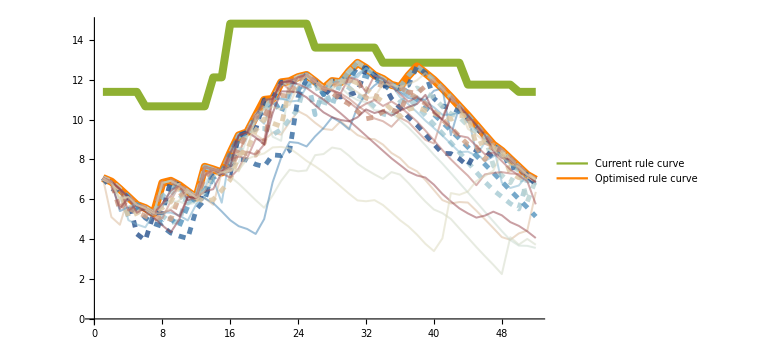

```mathematica
plotSolutionVsScenarios[fn_]:=Module[{data=Import[fn],nTimeSteps,nScenarios,cName,cOrder,cAvg,cSupport,colourScheme,plotLineColours,plotLineStyles,plotTimeStep},
nTimeSteps=Length[data]-4;
nScenarios=Length[data[[1]]]-2;
cName=nTimeSteps+1;
cOrder=nTimeSteps+2;
cAvg=nTimeSteps+3;
cSupport=nTimeSteps+4; 

(* Parameters for the scenarios. *)
colourScheme=ColorData["RedBlueTones"];

(* Parameters for the rule curves. *)
plotLineColours={ColorData[97,3],Orange}(*Table[ColorData[97,i^2],{i,1,2}]*);
plotLineStyles={{plotLineColours[[1]],Thickness[.01]},{plotLineColours[[2]],Thickness[.01]}};
plotTimeStep=If[nTimeSteps==12,"month",If[nTimeSteps==52,"week",If[nTimeSteps==365,"day"]]];

(* Actual plotting. The legends are drawn at the same time as the rule curves. *)
Return[
Show[
(* Rule curves. *)
ListPlot[
Table[data[[1;;nTimeSteps,i]],{i,1,2}],
PlotLegends->{
Placed[LineLegend[plotLineColours,Table[data[[cName,i]],{i,1,2}]],Left],
Placed[BarLegend[{colourScheme,{1,nScenarios}},LegendLabel->"Scenario rank,\n  from dryest\n   to wettest"],Right]
},
Joined->True,InterpolationOrder->1,
PlotStyle->plotLineStyles
],
(* Scenarios. *)
ListPlot[
Table[data[[1;;nTimeSteps,i]],{i,3,3+nScenarios-1}],
Joined->True,InterpolationOrder->1,
PlotStyle->Table[
{colourScheme[data[[cOrder,i]]/nScenarios],Opacity[If[data[[cSupport,i]]=="true",.8,.5]],Thickness[If[data[[cSupport,i]]=="true",.006,.0025]],If[data[[cSupport,i]]=="true",Dashed]},
{i,3,3+nScenarios-1}
],
PlotRange->{{1,nTimeSteps},{0,1.05Max[data[[1;;nTimeSteps,1]]]}},
Frame->True,
FrameLabel->{{"Stored volume [hm.b3]",None},{"Time ["<>plotTimeStep<>"]",None}}
],
(* Global parameters *)
ImageSize->Large
]
]
]

baseFolder="F:\\Univ\\_PhD\\Reservoirs\\Optimise_water_depth\\outputs\\cis-05pc\\plots\\";
plotSolutionVsScenarios[baseFolder<>"solution_safety_stochastic_merge_splitperscenario_DriestMonth.tsv"]
```

```mathematica
baseFolder="F:\\Univ\\_PhD\\Reservoirs\\Optimise_water_depth\\outputs\\cis-05pc\\plots\\";
Export[baseFolder<>#<>".Mathematica.png",plotSolutionVsScenarios[baseFolder<>#<>".tsv"],ImageResolution->300]&/@{"solution_safety_stochastic_merge_splitperscenario_DriestMonth","solution_safety_stochastic_merge_splitperscenario_DriestSixMonths","solution_safety_stochastic_merge_splitperscenario_DriestThreeMonths","solution_safety_stochastic_merge_splitperscenario_DrySeasonAverage","solution_safety_stochastic_merge_splitperscenario_WetSeasonAverage","solution_safety_stochastic_merge_splitperscenario_YearlyAverage"}
```

{F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestMonth.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestSixMonths.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestThreeMonths.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DrySeasonAverage.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_WetSeasonAverage.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_YearlyAverage.Mathematica.png}

```mathematica
analyseSupportScenariosSolutionVsScenarios[fn_]:=Module[{data=Import[fn],nTimeSteps,nScenarios,cName,cOrder,cAvg,cSupport,nSupportScenarios,averageSupportRank,averageNonSupportRank,averageSupportDischarge,averageNonSupportDischarge},
nTimeSteps=Length[data]-4;
nScenarios=Length[data[[1]]]-2;
cName=nTimeSteps+1;
cOrder=nTimeSteps+2;
cAvg=nTimeSteps+3;
cSupport=nTimeSteps+4; 

(* Perform a bit of analysis about the support scenarios. *)
nSupportScenarios=Total[data[[cSupport,3;;]]/.{"false"->0,"true"->1}];
averageSupportRank=Mean[Transpose[Select[Transpose[data],#[[cSupport]]=="true"&]][[cOrder]]];
averageNonSupportRank=Mean[Transpose[Select[Transpose[data],#[[cSupport]]=="false"&]][[cOrder]]];
averageSupportDischarge=Mean[Transpose[Select[Transpose[data],#[[cSupport]]=="true"&]][[cAvg]]];
averageNonSupportDischarge=Mean[Transpose[Select[Transpose[data],#[[cSupport]]=="false"&]][[cAvg]]];

(* Print the results. *)
Return["Number of scenarios: "<>ToString[nScenarios]<>"\n"<>
"Number of support scenarios: "<>ToString[nSupportScenarios]<>"\n"<>
"Number of nonsupport scenarios: "<>ToString[nScenarios-nSupportScenarios]<>"\n"<>
""<>"\n"<>
"Average rank of support scenarios: "<>ToString[N@averageSupportRank]<>"\n"<>
"Average rank of nonsupport scenarios: "<>ToString[N@averageNonSupportRank]<>"\n"<>
""<>"\n"<>
"Average discharge of support scenarios: "<>ToString[averageSupportDischarge]<>"\n"<>
"Average discharge of nonsupport scenarios: "<>ToString[averageNonSupportDischarge]
]
]
```

```mathematica
baseFolder="F:\\Univ\\_PhD\\Reservoirs\\Optimise_water_depth\\outputs\\cis-05pc\\plots\\";
Export[baseFolder<>#<>".Mathematica.txt",analyseSupportScenariosSolutionVsScenarios[baseFolder<>#<>".tsv"]]&/@{"solution_safety_stochastic_merge_splitperscenario_DriestMonth","solution_safety_stochastic_merge_splitperscenario_DriestSixMonths","solution_safety_stochastic_merge_splitperscenario_DriestThreeMonths","solution_safety_stochastic_merge_splitperscenario_DrySeasonAverage","solution_safety_stochastic_merge_splitperscenario_WetSeasonAverage","solution_safety_stochastic_merge_splitperscenario_YearlyAverage"}
```

{F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestMonth.Mathematica.txt,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestSixMonths.Mathematica.txt,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DriestThreeMonths.Mathematica.txt,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_DrySeasonAverage.Mathematica.txt,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_WetSeasonAverage.Mathematica.txt,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solution_safety_stochastic_merge_splitperscenario_YearlyAverage.Mathematica.txt}

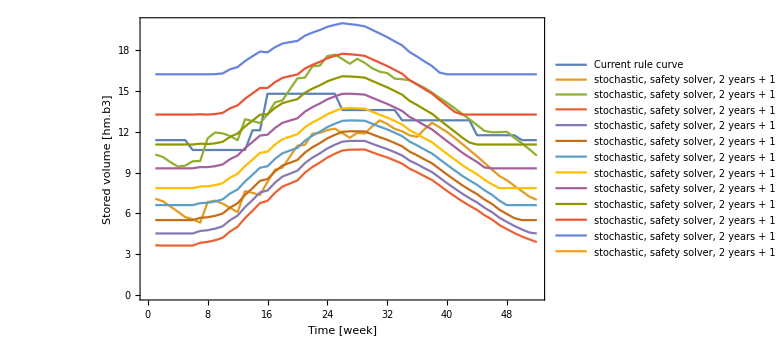

```mathematica
plotSolutions[fn_]:=Module[{data=Import[fn],nTimeSteps,nSolutions,cName,plotLineColours,plotTimeStep},
nTimeSteps=Length[data]-1;
nSolutions=Length[data[[1]]];
cName=nTimeSteps+1;

(* Parameters for the rule curves. *)
plotLineColours=Table[ColorData[97,i],{i,1,nSolutions}];
plotTimeStep=If[nTimeSteps==12,"month",If[nTimeSteps==52,"week",If[nTimeSteps==365,"day"]]];

(* Actual plotting. *)
Return[
Show[
(* Solutions. *)
ListPlot[
Table[data[[1;;nTimeSteps,i]],{i,1,nSolutions}],
PlotLegends->Table[data[[cName,i]],{i,1,nSolutions}],
Joined->True,InterpolationOrder->1,
PlotStyle->plotLineColours,
Frame->True,
FrameLabel->{{"Stored volume [hm.b3]",None},{"Time ["<>plotTimeStep<>"]",None}}
],
(* Global parameters *)
ImageSize->Large
]
]
]

baseFolder="F:\\Univ\\_PhD\\Reservoirs\\Optimise_water_depth\\outputs\\cis-05pc\\plots\\";
plotSolutions[baseFolder<>"solutions_safeMinimumRuleCurve.tsv"]
```

```mathematica
baseFolder="F:\\Univ\\_PhD\\Reservoirs\\Optimise_water_depth\\outputs\\cis-05pc\\plots\\";
Export[baseFolder<>#<>".Mathematica.png",plotSolutions[baseFolder<>#<>".tsv"],ImageResolution->300]&/@{"current_rule","solutions","solutions_minimumRuleCurve","solutions_safeMinimumRuleCurve"}
```

{F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\current_rule.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solutions.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solutions_minimumRuleCurve.Mathematica.png,F:\Univ\_PhD\Reservoirs\Optimise_water_depth\outputs\cis-05pc\plots\solutions_safeMinimumRuleCurve.Mathematica.png}